```mathematica
(*parameters shown in Table S1, Yamaguchi, Ode, Ueda, iScience 2020*)
{ka1, ka2, ka3, ka4, ka5, ka6, ka7, ka8, kb1, kb2, kb3, kb4, kb5, kb6, kb7, kb8, kma1, kma2, kma3, kma4, kma5, kma6, kma7, kma8, kmb1, kmb2, kmb3, kmb4, kmb5, kmb6, kmb7, kmb8} = {

47.24854606,103.9531911,10.08171512,1060.57115771,1060.57115771,10.08171512,103.9531911,47.24854606,209.36500373,10.6326728,19.66831864,12.42448634,12.42448634,19.66831864,10.6326728,209.36500373,1.47124828,0.00837871408,57.4110235,2.59762957,2.59762957,57.4110235,0.00837871408,1.47124828,87.7731777,38.4119873,4.31489994,0.0474636497,0.0474636497,4.31489994,38.4119873,87.7731777

};
```

```mathematica
(*total amount of substrate and enzymes*)
inisub=1000;
ktot=20;
ptot=20;
```

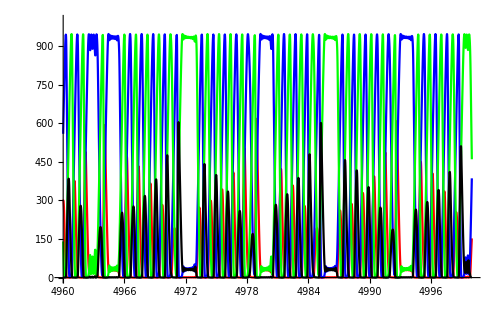

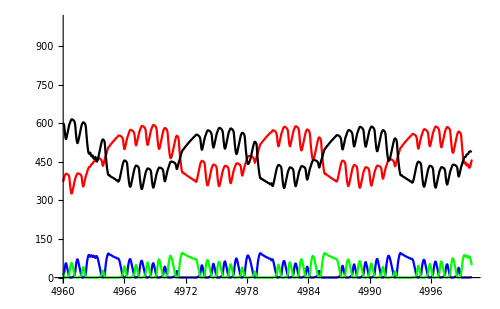

```mathematica
(*differential equation*)

(*numerical integration time*)
time=5000;

(*differential equation*)
s=NDSolve[
{
(*Sa ODEs*)
sa00'[t]==-(ka1/kma1+ka2/kma2)*sa00[t]*ktot/(1+sa00[t]/kma1+sa00[t]/kma2+sa01[t]/kma3+sa10[t]/kma4+sb00[t]/kmb1+sb00[t]/kmb2+sb01[t]/kmb3+sb10[t]/kmb4)+ka5*ptot/(1+sa01[t]/kma5+sa10[t]/kma6+sa11[t]/kma7+sa11[t]/kma8+sb01[t]/kmb5+sb10[t]/kmb6+sb11[t]/kmb7+sb11[t]/kmb8)*sa01[t]/kma5+ka6*ptot/(1+sa01[t]/kma5+sa10[t]/kma6+sa11[t]/kma7+sa11[t]/kma8+sb01[t]/kmb5+sb10[t]/kmb6+sb11[t]/kmb7+sb11[t]/kmb8)*sa10[t]/kma6,

sa11'[t]==-(ka7/kma7+ka8/kma8)*sa11[t]*ptot/(1+sa01[t]/kma5+sa10[t]/kma6+sa11[t]/kma7+sa11[t]/kma8+sb01[t]/kmb5+sb10[t]/kmb6+sb11[t]/kmb7+sb11[t]/kmb8)+ka3*ktot/(1+sa00[t]/kma1+sa00[t]/kma2+sa01[t]/kma3+sa10[t]/kma4+sb00[t]/kmb1+sb00[t]/kmb2+sb01[t]/kmb3+sb10[t]/kmb4)*sa01[t]/kma3+ka4*ktot/(1+sa00[t]/kma1+sa00[t]/kma2+sa01[t]/kma3+sa10[t]/kma4+sb00[t]/kmb1+sb00[t]/kmb2+sb01[t]/kmb3+sb10[t]/kmb4)*sa10[t]/kma4,


sa01'[t]==-ka3*sa01[t]*(ktot/(1+sa00[t]/kma1+sa00[t]/kma2+sa01[t]/kma3+sa10[t]/kma4+sb00[t]/kmb1+sb00[t]/kmb2+sb01[t]/kmb3+sb10[t]/kmb4))/kma3-ka5*sa01[t]*(ptot/(1+sa01[t]/kma5+sa10[t]/kma6+sa11[t]/kma7+sa11[t]/kma8+sb01[t]/kmb5+sb10[t]/kmb6+sb11[t]/kmb7+sb11[t]/kmb8))/kma5+ka1*ktot/(1+sa00[t]/kma1+sa00[t]/kma2+sa01[t]/kma3+sa10[t]/kma4+sb00[t]/kmb1+sb00[t]/kmb2+sb01[t]/kmb3+sb10[t]/kmb4)*sa00[t]/kma1+ka7*ptot/(1+sa01[t]/kma5+sa10[t]/kma6+sa11[t]/kma7+sa11[t]/kma8+sb01[t]/kmb5+sb10[t]/kmb6+sb11[t]/kmb7+sb11[t]/kmb8)*sa11[t]/kma7,

sa10'[t]==-ka4*sa10[t]*(ktot/(1+sa00[t]/kma1+sa00[t]/kma2+sa01[t]/kma3+sa10[t]/kma4+sb00[t]/kmb1+sb00[t]/kmb2+sb01[t]/kmb3+sb10[t]/kmb4))/kma4-ka6*sa10[t]*(ptot/(1+sa01[t]/kma5+sa10[t]/kma6+sa11[t]/kma7+sa11[t]/kma8+sb01[t]/kmb5+sb10[t]/kmb6+sb11[t]/kmb7+sb11[t]/kmb8))/kma6+ka2*ktot/(1+sa00[t]/kma1+sa00[t]/kma2+sa01[t]/kma3+sa10[t]/kma4+sb00[t]/kmb1+sb00[t]/kmb2+sb01[t]/kmb3+sb10[t]/kmb4)*sa00[t]/kma2+ka8*ptot/(1+sa01[t]/kma5+sa10[t]/kma6+sa11[t]/kma7+sa11[t]/kma8+sb01[t]/kmb5+sb10[t]/kmb6+sb11[t]/kmb7+sb11[t]/kmb8)*sa11[t]/kma8,

(*Sb ODEs*)

sb00'[t]==-(kb1/kmb1+kb2/kmb2)*sb00[t]*ktot/(1+sa00[t]/kma1+sa00[t]/kma2+sa01[t]/kma3+sa10[t]/kma4++sb00[t]/kmb1+sb00[t]/kmb2+sb01[t]/kmb3+sb10[t]/kmb4)+kb5*ptot/(1+sa01[t]/kma5+sa10[t]/kma6+sa11[t]/kma7+sa11[t]/kma8+sb01[t]/kmb5+sb10[t]/kmb6+sb11[t]/kmb7+sb11[t]/kmb8)*sb01[t]/kmb5+kb6*ptot/(1+sa01[t]/kma5+sa10[t]/kma6+sa11[t]/kma7+sa11[t]/kma8+sb01[t]/kmb5+sb10[t]/kmb6+sb11[t]/kmb7+sb11[t]/kmb8)*sb10[t]/kmb6,

sb11'[t]==-(kb7/kmb7+kb8/kmb8)*sb11[t]*ptot/(1+sa01[t]/kma5+sa10[t]/kma6+sa11[t]/kma7+sa11[t]/kma8+sb01[t]/kmb5+sb10[t]/kmb6+sb11[t]/kmb7+sb11[t]/kmb8)+kb3*ktot/(1+sa00[t]/kma1+sa00[t]/kma2+sa01[t]/kma3+sa10[t]/kma4++sb00[t]/kmb1+sb00[t]/kmb2+sb01[t]/kmb3+sb10[t]/kmb4)*sb01[t]/kmb3+kb4*ktot/(1+sa00[t]/kma1+sa00[t]/kma2+sa01[t]/kma3+sa10[t]/kma4++sb00[t]/kmb1+sb00[t]/kmb2+sb01[t]/kmb3+sb10[t]/kmb4)*sb10[t]/kmb4,


sb01'[t]==-kb3*sb01[t]*(ktot/(1+sa00[t]/kma1+sa00[t]/kma2+sa01[t]/kma3+sa10[t]/kma4++sb00[t]/kmb1+sb00[t]/kmb2+sb01[t]/kmb3+sb10[t]/kmb4))/kmb3-kb5*sb01[t]*(ptot/(1+sa01[t]/kma5+sa10[t]/kma6+sa11[t]/kma7+sa11[t]/kma8+sb01[t]/kmb5+sb10[t]/kmb6+sb11[t]/kmb7+sb11[t]/kmb8))/kmb5+kb1*ktot/(1+sa00[t]/kma1+sa00[t]/kma2+sa01[t]/kma3+sa10[t]/kma4++sb00[t]/kmb1+sb00[t]/kmb2+sb01[t]/kmb3+sb10[t]/kmb4)*sb00[t]/kmb1+kb7*ptot/(1+sa01[t]/kma5+sa10[t]/kma6+sa11[t]/kma7+sa11[t]/kma8+sb01[t]/kmb5+sb10[t]/kmb6+sb11[t]/kmb7+sb11[t]/kmb8)*sb11[t]/kmb7,

sb10'[t]==-kb4*sb10[t]*(ktot/(1+sa00[t]/kma1+sa00[t]/kma2+sa01[t]/kma3+sa10[t]/kma4++sb00[t]/kmb1+sb00[t]/kmb2+sb01[t]/kmb3+sb10[t]/kmb4))/kmb4-kb6*sb10[t]*(ptot/(1+sa01[t]/kma5+sa10[t]/kma6+sa11[t]/kma7+sa11[t]/kma8+sb01[t]/kmb5+sb10[t]/kmb6+sb11[t]/kmb7+sb11[t]/kmb8))/kmb6+kb2*ktot/(1+sa00[t]/kma1+sa00[t]/kma2+sa01[t]/kma3+sa10[t]/kma4++sb00[t]/kmb1+sb00[t]/kmb2+sb01[t]/kmb3+sb10[t]/kmb4)*sb00[t]/kmb2+kb8*ptot/(1+sa01[t]/kma5+sa10[t]/kma6+sa11[t]/kma7+sa11[t]/kma8+sb01[t]/kmb5+sb10[t]/kmb6+sb11[t]/kmb7+sb11[t]/kmb8)*sb11[t]/kmb8,




(*initial condition*)
sa00[0]==inisub,
sa10[0]==0,
sa11[0]==0,
sa01[0]==0,

sb00[0]==inisub,
sb10[0]==0,
sb11[0]==0,
sb01[0]==0

},

(*variables to be solved*)
{sa00, sa01,sa10,sa11,sb00, sb01,sb10,sb11},

(*ranges*)
{t,0,time}

];

(*plot Sa species*)
Plot[Evaluate[{sa00[t],sa10[t],sa01[t],sa11[t]}/.s],{t,4960,5000},PlotRange->{0,1000},PlotStyle->{Red,Blue,Green, Black},ImageSize->{500,500}]
(*plot Sb species*)
Plot[Evaluate[{sb00[t],sb10[t],sb01[t],sb11[t]}/.s],{t,4960,5000},PlotRange->{0,1000},PlotStyle->{Red,Blue,Green, Black},ImageSize->{500,500}]
```